# Spatially Adaptive Finite Volume Method For Moment Models

This Mathematica file implements a spatially adaptive finite volume method for moment models. The spatial adaptivity allows the simulation to use a different number of moments (and so different models) in different parts of the domain. Currently, the setting is the following: the domain is divided in 2 subdomains. In the left subdomain, the number of moments (=: ML) is smaller than the number of moments (=: MR) in the right subdomain.

## Simulation setup

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 100;
n=nxL+nxR;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

dx=(x2-x1)/(nxL+nxR);

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=6;
numberOfMomentsDifference=momentsRight-momentsLeft;

(* Choose initial values *)
m0=3;
m1=2;
m2=3;

epsilon=0.1;

momentsBig=2;

momentSmall=epsilon;

initialValuesLeft={m0,m1,m2};
initialValuesRight={m0,m1,m2};

For[i=4,i<=momentsLeft,i++,
initialValuesLeft=Append[initialValuesLeft,momentsBig];
initialValuesRight=Append[initialValuesRight,momentsBig];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
initialValuesRight=Append[initialValuesRight,momentSmall];
];

(* Choose Relaxation time *)
Relaxation=1;

W={};
For[i=0,i<nxL,i++,
values[i]=initialValuesLeft;
W=Join[W,values[i]];
];
values[nxL]=ArrayPad[initialValuesLeft,{0,numberOfMomentsDifference}]; (* Take initial values from the left and add zeroes *)
W=Join[W,values[nxL]];
For[i=1,i<=nxR+1,i++,
values[i+nxL]=initialValuesRight;
W=Join[W,values[i+nxL]];
];

(* Choose time step *)
dt=0.1dx;

time= 0.0;
step=0;

(* Choose end time *)
tend=1;
```

## Construction of the spatial discretization matrix

```mathematica
(* Define the model matrices *)
ALeft=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsLeft,momentsLeft}];
ARight=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsRight,momentsRight}];
ATilde=ARight;
ATilde[[-numberOfMomentsDifference;;-1,All]]=0;

(* Define the numerical viscosity matrices *)
QLeft=IdentityMatrix[momentsLeft];
QRight=IdentityMatrix[momentsRight];
QTilde=QRight;
QTilde[[-1,All]]=0;

Roe = ConstantArray[0,{n+2,n+2}];
Viscosity=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=nxL,j++,
Roe[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
]

For[j=nxL+1,j<=n+2,j++,
Roe[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
Viscosity[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
]


(* Rows corresponding to moment model of order ML *)
For[i=2,i<nxL,i++,
Roe[[i,i-1]]=ALeft;
Roe[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Roe[[i,i+1]]=-ALeft;
Viscosity[[i,i-1]]=-QLeft;
Viscosity[[i,i]]=2*QLeft;
Viscosity[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
Roe[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL,j++,
Roe[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
Roe[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
Viscosity[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

(* Row nxL (corresponds to vector nxL-1 because of the introduced ghost rows *) 
Roe[[nxL,nxL-1]]=ALeft;
Roe[[nxL,nxL]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Roe[[nxL,nxL+1]]=-ArrayPad[ALeft,{{0,0},{0,numberOfMomentsDifference}}];
Viscosity[[nxL,nxL-1]]=-QLeft;
Viscosity[[nxL,nxL]]=2*QLeft;
Viscosity[[nxL,nxL+1]]=-ArrayPad[QLeft,{{0,0},{0,numberOfMomentsDifference}}];

For[j=1,j<nxL-1,j++,
Roe[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
Viscosity[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
Roe[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
Viscosity[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];


(* Row nxL+1 (correspond to vector nxL because of the introduced  ghost rows *)
Roe[[nxL+1,nxL]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
Roe[[nxL+1,nxL+1]]=ConstantArray[0,{momentsRight,momentsRight}];
Roe[[nxL+1,nxL+2]]=-ATilde;
Viscosity[[nxL+1,nxL]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
Viscosity[[nxL+1,nxL+1]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
Viscosity[[nxL+1,nxL+2]]=-QTilde;

For[j=1,j<nxL,j++,
Roe[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+3,j<=n+2,j++,
Roe[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Row nxL+2 (corresponds to vector nxL+1 because of the introduced ghost rows *)

Roe[[nxL+2,nxL+1]]=ARight;
Roe[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
Roe[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
Roe[[nxL+2,nxL+3]]=-ARight;
Viscosity[[nxL+2,nxL+1]]=-QRight;
Viscosity[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
Viscosity[[nxL+2,nxL+2]]=2*QRight;
Viscosity[[nxL+2,nxL+3]]=-QRight;


For[j=1,j<=nxL,j++,
Roe[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+4,j<=n+2,j++,
Roe[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];


(* Rows corresponding to moment model of order MR (without the last one) *)
For[i=nxL+3,i<n+2,i++,
Roe[[i,i-1]]=ARight;
Roe[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
Roe[[i,i+1]]=-ARight;

Viscosity[[i,i-1]]=-QRight;
Viscosity[[i,i]]=2*QRight;
Viscosity[[i,i+1]]=-QRight;

For[j=1,j<=nxL,j++,
Roe[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<i-1,j++,
Roe[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
Roe[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];


(* Last rows are ghost rows *)
For[j=1,j<=nxL,j++,
Roe[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
Viscosity[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
Roe[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
Viscosity[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];


RoeFlatten = ArrayFlatten[Roe];
ViscosityFlatten = ArrayFlatten[Viscosity];

(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)

SourceMatrixLeft =SparseArray[{{i_,i_}/;i>=4:>1},{momentsLeft,momentsLeft}];
SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

SourceMatrix =ConstantArray[0,{n+2,n+2}];

For[i=1,i<=nxL,i++,
For[j=1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}]
];
SourceMatrix[[i,i]]=SourceMatrixLeft;
For[j=i+1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+1,j<=n+2,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

For[i=nxL+1,i<=n+2,i++,
For[j=1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}]
];
For[j=nxL+1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
SourceMatrix[[i,i]]=SourceMatrixRight;
For[j=i+1,j++,j<=n+2,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceTermVectorLeft={0,0,0};
SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
SourceTermVector={};
For[i=0,i<nxL,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorLeft];
];
For[i=nxL,i<=n+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorRight];
]
(* Obtain source term vector *)
SourceTermVector=-1/Relaxation*SourceTermVector;
SourceTermMatrix=DiagonalMatrix[SourceTermVector];

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

(* Obtain transport part of spatial discretization matrix from Roe block matrix and viscosity block matrix *)
BigAMatrix=-1.0/(2*dx)*(Roe+Viscosity);
BigAMatrixFlatten = -1.0/(2*dx)*(RoeFlatten+ViscosityFlatten);

M=BigAMatrixFlatten;
```

## Simulation

```mathematica
While[time<tend,
(* Compute the values of the point s0 along the path *)
norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];

(* s0=0; *)

(* THE SYSTEM MATRIX HERE IS A WEIGHTED SUM OF THE BIGGER MATRIX AND THE SMALLER MATRIX *)


WeightedSumRoe=s0*ATilde+(1-s0)*ARight;
WeightedSumRoe[[All,-numberOfMomentsDifference;;-1]]=0;
WeightedSumViscosity=s0*QTilde+(1-s0)*QRight;
WeightedSumViscosity[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffA=ATilde-ARight;
modelDiffQ=QTilde-QRight;
modelDiffA[[All,-numberOfMomentsDifference;;-1]]=0;
modelDiffQ[[All,-numberOfMomentsDifference;;-1]]=0;
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(WeightedSumRoe-WeightedSumViscosity);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(s0*modelDiffA+2*QRight+s0*(modelDiffQ));
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ARight-QRight);



(* USING THE BIGGER MATRIX *)
(*
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(ARight-QRight);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*QRight);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ARight-QRight);
*)

(* USING THE SMALLER MATRIX *)
(*
BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]);
*)

BigAMatrixFlatten=ArrayFlatten[BigAMatrix];

(* Transport step *)
W=W+dt*BigAMatrixFlatten.W;

(* Relaxation step *)
W=DiagonalMatrix[SourceTermVector].W;

time = time+dt;
step++;
]
```

## Numerical data post processing

```mathematica
(* Collect values that correspond to the same moments *)
```

```mathematica
moments=Table[moment[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,moment[i]={}];

For[i=0,i<nxL,i++,
For[j=0,j<momentsRight-numberOfMomentsDifference,j++,
moment[j]=Append[moment[j],W[[momentsLeft*i+j+1]]]
]
]
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
moment[j]=Append[moment[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
]
```

## Plotting

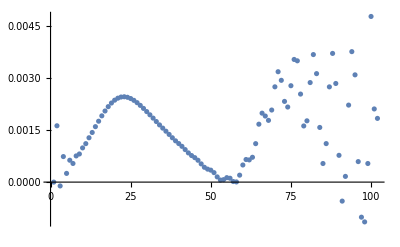

```mathematica
ListPlot[moment[7]]
```

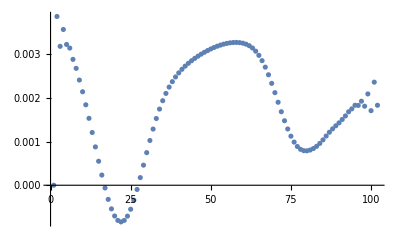

```mathematica
ListPlot[moment[5]]
```

## Stability analysis

```mathematica
StabilityMatrix = BigAMatrixFlatten+SourceTermMatrix;
(*Eigenvalues[StabilityMatrix]*)
(*CharPol[λ_]=CharacteristicPolynomial[StabilityMatrix,λ];*)
```

```mathematica
Eigenvalues[StabilityMatrix]
```

{-11.6953+32.5739 ⅈ,-11.6953-32.5739 ⅈ,-11.4315+32.6626 ⅈ,-11.4315-32.6626 ⅈ,-11.9587+32.4531 ⅈ,-11.9587-32.4531 ⅈ,-11.1675+32.719 ⅈ,-11.1675-32.719 ⅈ,-12.2215+32.3004 ⅈ,-12.2215-32.3004 ⅈ,-10.9033+32.743 ⅈ,-10.9033-32.743 ⅈ,-12.4835+32.116 ⅈ,-12.4835-32.116 ⅈ,-10.6391+32.7346 ⅈ,-10.6391-32.7346 ⅈ,-12.7446+31.9002 ⅈ,-12.7446-31.9002 ⅈ,-10.3749+32.6937 ⅈ,-10.3749-32.6937 ⅈ,-13.0045+31.6533 ⅈ,-13.0045-31.6533 ⅈ,-10.1109+32.6205 ⅈ,-10.1109-32.6205 ⅈ,-13.263+31.3756 ⅈ,-13.263-31.3756 ⅈ,-9.84722+32.5151 ⅈ,-9.84722-32.5151 ⅈ,-13.5198+31.0675 ⅈ,-13.5198-31.0675 ⅈ,-9.58398+32.3776 ⅈ,-9.58398-32.3776 ⅈ,-13.7746+30.7293 ⅈ,-13.7746-30.7293 ⅈ,-9.32137+32.2084 ⅈ,-9.32137-32.2084 ⅈ,-14.0273+30.3615 ⅈ,-14.0273-30.3615 ⅈ,-9.05959+32.0076 ⅈ,-9.05959-32.0076 ⅈ,-14.2775+29.9643 ⅈ,-14.2775-29.9643 ⅈ,-8.79886+31.7757 ⅈ,-8.79886-31.7757 ⅈ,-14.525+29.5383 ⅈ,-14.525-29.5383 ⅈ,-8.53942+31.5127 ⅈ,-8.53942-31.5127 ⅈ,-14.7696+29.0839 ⅈ,-14.7696-29.0839 ⅈ,-15.0109+28.6016 ⅈ,-15.0109-28.6016 ⅈ,-8.28151+31.2192 ⅈ,-8.28151-31.2192 ⅈ,-15.2487+28.0918 ⅈ,-15.2487-28.0918 ⅈ,-8.02537+30.8955 ⅈ,-8.02537-30.8955 ⅈ,-15.4828+27.555 ⅈ,-15.4828-27.555 ⅈ,-7.77127+30.5418 ⅈ,-7.77127-30.5418 ⅈ,-15.7128+26.9919 ⅈ,-15.7128-26.9919 ⅈ,-7.51946+30.1587 ⅈ,-7.51946-30.1587 ⅈ,-15.9386+26.4029 ⅈ,-15.9386-26.4029 ⅈ,-7.27019+29.7466 ⅈ,-7.27019-29.7466 ⅈ,-16.1599+25.7887 ⅈ,-16.1599-25.7887 ⅈ,-7.02374+29.3058 ⅈ,-7.02374-29.3058 ⅈ,-16.3765+25.1497 ⅈ,-16.3765-25.1497 ⅈ,-6.78035+28.8369 ⅈ,-6.78035-28.8369 ⅈ,-16.588+24.4865 ⅈ,-16.588-24.4865 ⅈ,-16.7943+23.7999 ⅈ,-16.7943-23.7999 ⅈ,-6.5403+28.3404 ⅈ,-6.5403-28.3404 ⅈ,-16.9952+23.0902 ⅈ,-16.9952-23.0902 ⅈ,-6.30385+27.8167 ⅈ,-6.30385-27.8167 ⅈ,-17.1905+22.3582 ⅈ,-17.1905-22.3582 ⅈ,-6.07127+27.2664 ⅈ,-6.07127-27.2664 ⅈ,-17.3802+21.6045 ⅈ,-17.3802-21.6045 ⅈ,-5.84284+26.69 ⅈ,-5.84284-26.69 ⅈ,-17.5639+20.8298 ⅈ,-17.5639-20.8298 ⅈ,-17.7418+20.0348 ⅈ,-17.7418-20.0348 ⅈ,-5.61881+26.0882 ⅈ,-5.61881-26.0882 ⅈ,-17.9138+19.2201 ⅈ,-17.9138-19.2201 ⅈ,-5.39948+25.4614 ⅈ,-5.39948-25.4614 ⅈ,-18.0797+18.3867 ⅈ,-18.0797-18.3867 ⅈ,-12.381+22.45 ⅈ,-12.381-22.45 ⅈ,-12.0907+22.6028 ⅈ,-12.0907-22.6028 ⅈ,-12.6694+22.275 ⅈ,-12.6694-22.275 ⅈ,-11.7987+22.7333 ⅈ,-11.7987-22.7333 ⅈ,-12.9556+22.0781 ⅈ,-12.9556-22.0781 ⅈ,-11.5054+22.8413 ⅈ,-11.5054-22.8413 ⅈ,-13.2394+21.8594 ⅈ,-13.2394-21.8594 ⅈ,-11.211+22.9267 ⅈ,-11.211-22.9267 ⅈ,-13.5205+21.6192 ⅈ,-13.5205-21.6192 ⅈ,-10.9158+22.9894 ⅈ,-10.9158-22.9894 ⅈ,-13.7985+21.3578 ⅈ,-13.7985-21.3578 ⅈ,-10.6199+23.0293 ⅈ,-10.6199-23.0293 ⅈ,-5.1851+24.8103 ⅈ,-5.1851-24.8103 ⅈ,-14.0733+21.0753 ⅈ,-14.0733-21.0753 ⅈ,-18.2396+17.5353 ⅈ,-18.2396-17.5353 ⅈ,-10.3238+23.0464 ⅈ,-10.3238-23.0464 ⅈ,-14.3445+20.7721 ⅈ,-14.3445-20.7721 ⅈ,-14.612+20.4486 ⅈ,-14.612-20.4486 ⅈ,-10.0276+23.0406 ⅈ,-10.0276-23.0406 ⅈ,-14.8753+20.1049 ⅈ,-14.8753-20.1049 ⅈ,-9.73156+23.012 ⅈ,-9.73156-23.012 ⅈ,-15.1343+19.7416 ⅈ,-15.1343-19.7416 ⅈ,-9.436+22.9606 ⅈ,-9.436-22.9606 ⅈ,-18.3934+16.6669 ⅈ,-18.3934-16.6669 ⅈ,-15.3887+19.3588 ⅈ,-15.3887-19.3588 ⅈ,-9.14116+22.8865 ⅈ,-9.14116-22.8865 ⅈ,-4.97595+24.1353 ⅈ,-4.97595-24.1353 ⅈ,-15.6382+18.957 ⅈ,-15.6382-18.957 ⅈ,-8.84729+22.7897 ⅈ,-8.84729-22.7897 ⅈ,-15.8826+18.5367 ⅈ,-15.8826-18.5367 ⅈ,-18.5411+15.7822 ⅈ,-18.5411-15.7822 ⅈ,-16.1217+18.0981 ⅈ,-16.1217-18.0981 ⅈ,-8.55465+22.6703 ⅈ,-8.55465-22.6703 ⅈ,-16.3551+17.6417 ⅈ,-16.3551-17.6417 ⅈ,-8.26353+22.5285 ⅈ,-8.26353-22.5285 ⅈ,-4.77225+23.4371 ⅈ,-4.77225-23.4371 ⅈ,-18.6826+14.8823 ⅈ,-18.6826-14.8823 ⅈ,-16.5828+17.168 ⅈ,-16.5828-17.168 ⅈ,-7.97418+22.3645 ⅈ,-7.97418-22.3645 ⅈ,-16.8045+16.6774 ⅈ,-16.8045-16.6774 ⅈ,-17.02+16.1703 ⅈ,-17.02-16.1703 ⅈ,-7.68687+22.1784 ⅈ,-7.68687-22.1784 ⅈ,-18.8178+13.968 ⅈ,-18.8178-13.968 ⅈ,-17.229+15.6474 ⅈ,-17.229-15.6474 ⅈ,-7.40189+21.9705 ⅈ,-7.40189-21.9705 ⅈ,-4.57421+22.7163 ⅈ,-4.57421-22.7163 ⅈ,-17.4314+15.1089 ⅈ,-17.4314-15.1089 ⅈ,-18.9468+13.0403 ⅈ,-18.9468-13.0403 ⅈ,-7.1195+21.7409 ⅈ,-7.1195-21.7409 ⅈ,-17.6271+14.5556 ⅈ,-17.6271-14.5556 ⅈ,-17.8158+13.988 ⅈ,-17.8158-13.988 ⅈ,-19.0697+12.1 ⅈ,-19.0697-12.1 ⅈ,-6.83998+21.4899 ⅈ,-6.83998-21.4899 ⅈ,-17.9971+13.4063 ⅈ,-17.9971-13.4063 ⅈ,-4.38199+21.9734 ⅈ,-4.38199-21.9734 ⅈ,-18.172+12.8113 ⅈ,-18.172-12.8113 ⅈ,-6.56361+21.2177 ⅈ,-6.56361-21.2177 ⅈ,-19.1854+11.1485 ⅈ,-19.1854-11.1485 ⅈ,-18.3386+12.205 ⅈ,-18.3386-12.205 ⅈ,-13.8967+17.0197 ⅈ,-13.8967-17.0197 ⅈ,-13.6271+17.2343 ⅈ,-13.6271-17.2343 ⅈ,-14.163+16.7886 ⅈ,-14.163-16.7886 ⅈ,-13.3545+17.4323 ⅈ,-13.3545-17.4323 ⅈ,-14.4258+16.5412 ⅈ,-14.4258-16.5412 ⅈ,-13.0792+17.6133 ⅈ,-13.0792-17.6133 ⅈ,-14.6849+16.2778 ⅈ,-14.6849-16.2778 ⅈ,-12.8014+17.7772 ⅈ,-12.8014-17.7772 ⅈ,-14.94+15.9986 ⅈ,-14.94-15.9986 ⅈ,-12.5213+17.9238 ⅈ,-12.5213-17.9238 ⅈ,-6.29065+20.9247 ⅈ,-6.29065-20.9247 ⅈ,-15.1909+15.704 ⅈ,-15.1909-15.704 ⅈ,-18.4963+11.5838 ⅈ,-18.4963-11.5838 ⅈ,-19.2974+10.1841 ⅈ,-19.2974-10.1841 ⅈ,-12.2392+18.053 ⅈ,-12.2392-18.053 ⅈ,-15.4374+15.3942 ⅈ,-15.4374-15.3942 ⅈ,-15.6791+15.0695 ⅈ,-15.6791-15.0695 ⅈ,-11.9555+18.1647 ⅈ,-11.9555-18.1647 ⅈ,-15.9159+14.7302 ⅈ,-15.9159-14.7302 ⅈ,-11.6702+18.2587 ⅈ,-11.6702-18.2587 ⅈ,-18.6513+10.9512 ⅈ,-18.6513-10.9512 ⅈ,-16.1477+14.3766 ⅈ,-16.1477-14.3766 ⅈ,-4.19571+21.2089 ⅈ,-4.19571-21.2089 ⅈ,-11.3837+18.335 ⅈ,-11.3837-18.335 ⅈ,-16.3741+14.0093 ⅈ,-16.3741-14.0093 ⅈ,-11.0963+18.3934 ⅈ,-11.0963-18.3934 ⅈ,-19.3999+9.21735 ⅈ,-19.3999-9.21735 ⅈ,-16.5948+13.6284 ⅈ,-16.5948-13.6284 ⅈ,-6.02138+20.6112 ⅈ,-6.02138-20.6112 ⅈ,-18.7948+10.3151 ⅈ,-18.7948-10.3151 ⅈ,-16.8098+13.2341 ⅈ,-16.8098-13.2341 ⅈ,-10.8081+18.4339 ⅈ,-10.8081-18.4339 ⅈ,-17.0191+12.8271 ⅈ,-17.0191-12.8271 ⅈ,-18.9236+9.65929 ⅈ,-18.9236-9.65929 ⅈ,-10.5195+18.4565 ⅈ,-10.5195-18.4565 ⅈ,-17.2222+12.4082 ⅈ,-17.2222-12.4082 ⅈ,-19.4977+8.22263 ⅈ,-19.4977-8.22263 ⅈ,-17.4181+11.9772 ⅈ,-17.4181-11.9772 ⅈ,-10.2307+18.461 ⅈ,-10.2307-18.461 ⅈ,-5.75606+20.2773 ⅈ,-5.75606-20.2773 ⅈ,-19.0577+8.98782 ⅈ,-19.0577-8.98782 ⅈ,-17.6078+11.533 ⅈ,-17.6078-11.533 ⅈ,-17.7932+11.0783 ⅈ,-17.7932-11.0783 ⅈ,-9.942+18.4477 ⅈ,-9.942-18.4477 ⅈ,-20.9272+0. ⅈ,-19.1861+8.33157 ⅈ,-19.1861-8.33157 ⅈ,-19.6015+7.25092 ⅈ,-19.6015-7.25092 ⅈ,-17.9709+10.6166 ⅈ,-17.9709-10.6166 ⅈ,-20.8462+0. ⅈ,-4.01541+20.4237 ⅈ,-4.01541-20.4237 ⅈ,-9.65358+18.4163 ⅈ,-9.65358-18.4163 ⅈ,-18.136+10.1432 ⅈ,-18.136-10.1432 ⅈ,-19.2835+7.65182 ⅈ,-19.2835-7.65182 ⅈ,-18.2955+9.6521 ⅈ,-18.2955-9.6521 ⅈ,-5.49497+19.9236 ⅈ,-5.49497-19.9236 ⅈ,-19.6566+6.23861 ⅈ,-19.6566-6.23861 ⅈ,-20.6201+0. ⅈ,-9.36572+18.367 ⅈ,-9.36572-18.367 ⅈ,-18.4591+9.15264 ⅈ,-18.4591-9.15264 ⅈ,-19.384+6.95371 ⅈ,-19.384-6.95371 ⅈ,-18.6152+8.66016 ⅈ,-18.6152-8.66016 ⅈ,-19.4986+6.25367 ⅈ,-19.4986-6.25367 ⅈ,-19.7922+5.23685 ⅈ,-19.7922-5.23685 ⅈ,-18.7425+8.16117 ⅈ,-18.7425-8.16117 ⅈ,-20.4256+0.338795 ⅈ,-20.4256-0.338795 ⅈ,-9.07869+18.2999 ⅈ,-9.07869-18.2999 ⅈ,-19.5807+5.55969 ⅈ,-19.5807-5.55969 ⅈ,-18.8567+7.62677 ⅈ,-18.8567-7.62677 ⅈ,-20.2962+0.38194 ⅈ,-20.2962-0.38194 ⅈ,-20.2485+1.23974 ⅈ,-20.2485-1.23974 ⅈ,-19.8355+4.22698 ⅈ,-19.8355-4.22698 ⅈ,-18.9967+7.07293 ⅈ,-18.9967-7.07293 ⅈ,-19.6648+4.85759 ⅈ,-19.6648-4.85759 ⅈ,-20.2355+0.608033 ⅈ,-20.2355-0.608033 ⅈ,-5.23837+19.5503 ⅈ,-5.23837-19.5503 ⅈ,-19.1468+6.55282 ⅈ,-19.1468-6.55282 ⅈ,-8.79275+18.2149 ⅈ,-8.79275-18.2149 ⅈ,-20.0683+2.20144 ⅈ,-20.0683-2.20144 ⅈ,-19.9338+3.17959 ⅈ,-19.9338-3.17959 ⅈ,-19.2569+6.05226 ⅈ,-19.2569-6.05226 ⅈ,-20.1594+0.854095 ⅈ,-20.1594-0.854095 ⅈ,-20.168+0.543017 ⅈ,-20.168-0.543017 ⅈ,-20.1556+0.308895 ⅈ,-20.1556-0.308895 ⅈ,-20.1377+0.73345 ⅈ,-20.1377-0.73345 ⅈ,-19.7101+4.1808 ⅈ,-19.7101-4.1808 ⅈ,-20.1028+1.04517 ⅈ,-20.1028-1.04517 ⅈ,-20.0787+0.98297 ⅈ,-20.0787-0.98297 ⅈ,-20.0586+1.17573 ⅈ,-20.0586-1.17573 ⅈ,-20.0778+0. ⅈ,-20.0284+1.32723 ⅈ,-20.0284-1.32723 ⅈ,-19.2977+5.51078 ⅈ,-19.2977-5.51078 ⅈ,-19.9576+2.00908 ⅈ,-19.9576-2.00908 ⅈ,-19.877+2.66965 ⅈ,-19.877-2.66965 ⅈ,-19.7659+3.34474 ⅈ,-19.7659-3.34474 ⅈ,-19.5515+4.31589 ⅈ,-19.5515-4.31589 ⅈ,-8.50814+18.1123 ⅈ,-8.50814-18.1123 ⅈ,-19.7149+3.34792 ⅈ,-19.7149-3.34792 ⅈ,-3.84113+19.6182 ⅈ,-3.84113-19.6182 ⅈ,-19.9283+1.57228 ⅈ,-19.9283-1.57228 ⅈ,-19.3781+4.89318 ⅈ,-19.3781-4.89318 ⅈ,-19.6215+3.78798 ⅈ,-19.6215-3.78798 ⅈ,-19.9269+1.46095 ⅈ,-19.9269-1.46095 ⅈ,-19.9182+1.31812 ⅈ,-19.9182-1.31812 ⅈ,-19.8467+1.65827 ⅈ,-19.8467-1.65827 ⅈ,-19.8361+1.75054 ⅈ,-19.8361-1.75054 ⅈ,-19.8375+0.0520299 ⅈ,-19.8375-0.0520299 ⅈ,-19.7258+2.08638 ⅈ,-19.7258-2.08638 ⅈ,-19.6479+2.68611 ⅈ,-19.6479-2.68611 ⅈ,-19.7318+1.84812 ⅈ,-19.7318-1.84812 ⅈ,-19.7129+1.96233 ⅈ,-19.7129-1.96233 ⅈ,-4.98649+19.1578 ⅈ,-4.98649-19.1578 ⅈ,-8.22512+17.992 ⅈ,-8.22512-17.992 ⅈ,-19.7474+1.1853 ⅈ,-19.7474-1.1853 ⅈ,-19.7468+0.781771 ⅈ,-19.7468-0.781771 ⅈ,-19.758+0.407737 ⅈ,-19.758-0.407737 ⅈ,-19.639+2.17259 ⅈ,-19.639-2.17259 ⅈ,-19.6853+1.48019 ⅈ,-19.6853-1.48019 ⅈ,-19.5301+2.37403 ⅈ,-19.5301-2.37403 ⅈ,-19.5511+2.03338 ⅈ,-19.5511-2.03338 ⅈ,-19.4352+2.59823 ⅈ,-19.4352-2.59823 ⅈ,-19.4423+2.22115 ⅈ,-19.4423-2.22115 ⅈ,-7.94395+17.8543 ⅈ,-7.94395-17.8543 ⅈ,-19.3836+2.40722 ⅈ,-19.3836-2.40722 ⅈ,-19.3072+2.80292 ⅈ,-19.3072-2.80292 ⅈ,-19.1772+3.0121 ⅈ,-19.1772-3.0121 ⅈ,-19.2119+2.55147 ⅈ,-19.2119-2.55147 ⅈ,-4.73962+18.7464 ⅈ,-4.73962-18.7464 ⅈ,-19.0449+3.21392 ⅈ,-19.0449-3.21392 ⅈ,-7.66488+17.6992 ⅈ,-7.66488-17.6992 ⅈ,-19.0778+2.73738 ⅈ,-19.0778-2.73738 ⅈ,-18.8989+3.41219 ⅈ,-18.8989-3.41219 ⅈ,-18.9357+2.88216 ⅈ,-18.9357-2.88216 ⅈ,-3.67287+18.7933 ⅈ,-3.67287-18.7933 ⅈ,-18.7462+3.60933 ⅈ,-18.7462-3.60933 ⅈ,-7.38818+17.5269 ⅈ,-7.38818-17.5269 ⅈ,-18.7701+3.04643 ⅈ,-18.7701-3.04643 ⅈ,-18.5858+3.80133 ⅈ,-18.5858-3.80133 ⅈ,-18.6118+3.20109 ⅈ,-18.6118-3.20109 ⅈ,-4.49799+18.3165 ⅈ,-4.49799-18.3165 ⅈ,-18.4165+3.98979 ⅈ,-18.4165-3.98979 ⅈ,-7.11408+17.3377 ⅈ,-7.11408-17.3377 ⅈ,-18.4357+3.35076 ⅈ,-18.4357-3.35076 ⅈ,-18.2396+4.17454 ⅈ,-18.2396-4.17454 ⅈ,-18.2569+3.50106 ⅈ,-18.2569-3.50106 ⅈ,-18.055+4.3549 ⅈ,-18.055-4.3549 ⅈ,-6.84284+17.1316 ⅈ,-6.84284-17.1316 ⅈ,-18.0693+3.64419 ⅈ,-18.0693-3.64419 ⅈ,-17.8628+4.53101 ⅈ,-17.8628-4.53101 ⅈ,-4.26157+17.8691 ⅈ,-4.26157-17.8691 ⅈ,-3.51059+17.9499 ⅈ,-3.51059-17.9499 ⅈ,-17.6633+4.70264 ⅈ,-17.6633-4.70264 ⅈ,-17.874+3.78602 ⅈ,-17.874-3.78602 ⅈ,-6.57472+16.909 ⅈ,-6.57472-16.909 ⅈ,-17.4565+4.86959 ⅈ,-17.4565-4.86959 ⅈ,-17.6726+3.92296 ⅈ,-17.6726-3.92296 ⅈ,-17.2427+5.03174 ⅈ,-17.2427-5.03174 ⅈ,-17.4635+4.05636 ⅈ,-17.4635-4.05636 ⅈ,-4.03222+17.4031 ⅈ,-4.03222-17.4031 ⅈ,-6.30996+16.67 ⅈ,-6.30996-16.67 ⅈ,-17.0222+5.18891 ⅈ,-17.0222-5.18891 ⅈ,-17.2482+4.1858 ⅈ,-17.2482-4.1858 ⅈ,-16.795+5.34095 ⅈ,-16.795-5.34095 ⅈ,-17.0261+4.311 ⅈ,-17.0261-4.311 ⅈ,-6.0488+16.4149 ⅈ,-6.0488-16.4149 ⅈ,-16.5615+5.48773 ⅈ,-16.5615-5.48773 ⅈ,-3.35483+17.0884 ⅈ,-3.35483-17.0884 ⅈ,-16.7979+4.43211 ⅈ,-16.7979-4.43211 ⅈ,-3.80384+16.9202 ⅈ,-3.80384-16.9202 ⅈ,-16.3219+5.62909 ⅈ,-16.3219-5.62909 ⅈ,-16.5635+4.54882 ⅈ,-16.5635-4.54882 ⅈ,-5.79148+16.1439 ⅈ,-5.79148-16.1439 ⅈ,-16.0763+5.76491 ⅈ,-16.0763-5.76491 ⅈ,-16.3232+4.66115 ⅈ,-16.3232-4.66115 ⅈ,-15.8251+5.89504 ⅈ,-15.8251-5.89504 ⅈ,-3.59359+16.4265 ⅈ,-3.59359-16.4265 ⅈ,-5.53829+15.8573 ⅈ,-5.53829-15.8573 ⅈ,-16.0774+4.76894 ⅈ,-16.0774-4.76894 ⅈ,-15.5684+6.01938 ⅈ,-15.5684-6.01938 ⅈ,-15.8261+4.87212 ⅈ,-15.8261-4.87212 ⅈ,-3.20029+16.2152 ⅈ,-3.20029-16.2152 ⅈ,-15.3066+6.13779 ⅈ,-15.3066-6.13779 ⅈ,-5.28937+15.5553 ⅈ,-5.28937-15.5553 ⅈ,-15.5697+4.9706 ⅈ,-15.5697-4.9706 ⅈ,-15.0398+6.25016 ⅈ,-15.0398-6.25016 ⅈ,-3.37874+15.889 ⅈ,-3.37874-15.889 ⅈ,-15.3083+5.06427 ⅈ,-15.3083-5.06427 ⅈ,-14.7683+6.35638 ⅈ,-14.7683-6.35638 ⅈ,-5.04486+15.2384 ⅈ,-5.04486-15.2384 ⅈ,-15.0422+5.15306 ⅈ,-15.0422-5.15306 ⅈ,-14.4925+6.45636 ⅈ,-14.4925-6.45636 ⅈ,-3.16869+15.4304 ⅈ,-3.16869-15.4304 ⅈ,-14.7717+5.23689 ⅈ,-14.7717-5.23689 ⅈ,-4.80559+14.907 ⅈ,-4.80559-14.907 ⅈ,-14.2125+6.54999 ⅈ,-14.2125-6.54999 ⅈ,-3.03923+15.2665 ⅈ,-3.03923-15.2665 ⅈ,-14.4971+5.31569 ⅈ,-14.4971-5.31569 ⅈ,-13.9287+6.63718 ⅈ,-13.9287-6.63718 ⅈ,-4.57131+14.5603 ⅈ,-4.57131-14.5603 ⅈ,-13.6413+6.71785 ⅈ,-13.6413-6.71785 ⅈ,-14.2185+5.38938 ⅈ,-14.2185-5.38938 ⅈ,-3.02294+14.8205 ⅈ,-3.02294-14.8205 ⅈ,-13.3505+6.79191 ⅈ,-13.3505-6.79191 ⅈ,-13.9362+5.45789 ⅈ,-13.9362-5.45789 ⅈ,-4.34057+14.2 ⅈ,-4.34057-14.2 ⅈ,-2.84744+14.4775 ⅈ,-2.84744-14.4775 ⅈ,-13.0568+6.85931 ⅈ,-13.0568-6.85931 ⅈ,-13.6506+5.52117 ⅈ,-13.6506-5.52117 ⅈ,-12.7603+6.91997 ⅈ,-12.7603-6.91997 ⅈ,-13.3619+5.57916 ⅈ,-13.3619-5.57916 ⅈ,-2.81522+14.1674 ⅈ,-2.81522-14.1674 ⅈ,-4.1167+13.8289 ⅈ,-4.1167-13.8289 ⅈ,-12.4614+6.97384 ⅈ,-12.4614-6.97384 ⅈ,-13.0703+5.6318 ⅈ,-13.0703-5.6318 ⅈ,-12.1603+7.02086 ⅈ,-12.1603-7.02086 ⅈ,-2.70997+13.7549 ⅈ,-2.70997-13.7549 ⅈ,-3.90295+13.441 ⅈ,-3.90295-13.441 ⅈ,-12.7761+5.67905 ⅈ,-12.7761-5.67905 ⅈ,-11.8573+7.06098 ⅈ,-11.8573-7.06098 ⅈ,-12.4797+5.72086 ⅈ,-12.4797-5.72086 ⅈ,-2.6094+13.4405 ⅈ,-2.6094-13.4405 ⅈ,-11.5528+7.09418 ⅈ,-11.5528-7.09418 ⅈ,-3.6881+13.0334 ⅈ,-3.6881-13.0334 ⅈ,-12.1813+5.75719 ⅈ,-12.1813-5.75719 ⅈ,-11.247+7.1204 ⅈ,-11.247-7.1204 ⅈ,-2.54738+13.0562 ⅈ,-2.54738-13.0562 ⅈ,-11.8811+5.78802 ⅈ,-11.8811-5.78802 ⅈ,-3.46883+12.6264 ⅈ,-3.46883-12.6264 ⅈ,-10.9402+7.13964 ⅈ,-10.9402-7.13964 ⅈ,-11.5795+5.81332 ⅈ,-11.5795-5.81332 ⅈ,-2.44799+12.6797 ⅈ,-2.44799-12.6797 ⅈ,-10.6327+7.15187 ⅈ,-10.6327-7.15187 ⅈ,-11.2768+5.83306 ⅈ,-11.2768-5.83306 ⅈ,-3.28007+12.2216 ⅈ,-3.28007-12.2216 ⅈ,-2.37621+12.3383 ⅈ,-2.37621-12.3383 ⅈ,-10.3249+7.15708 ⅈ,-10.3249-7.15708 ⅈ,-10.9731+5.84722 ⅈ,-10.9731-5.84722 ⅈ,-10.017+7.15526 ⅈ,-10.017-7.15526 ⅈ,-3.11544+11.7665 ⅈ,-3.11544-11.7665 ⅈ,-10.6689+5.8558 ⅈ,-10.6689-5.8558 ⅈ,-2.29545+11.9315 ⅈ,-2.29545-11.9315 ⅈ,-9.70932+7.14642 ⅈ,-9.70932-7.14642 ⅈ,-10.3645+5.85878 ⅈ,-10.3645-5.85878 ⅈ,-9.40217+7.13056 ⅈ,-9.40217-7.13056 ⅈ,-2.22768+11.5839 ⅈ,-2.22768-11.5839 ⅈ,-10.06+5.85616 ⅈ,-10.06-5.85616 ⅈ,-2.90168+11.2709 ⅈ,-2.90168-11.2709 ⅈ,-9.09585+7.1077 ⅈ,-9.09585-7.1077 ⅈ,-2.14959+11.1911 ⅈ,-2.14959-11.1911 ⅈ,-9.75578+5.84795 ⅈ,-9.75578-5.84795 ⅈ,-8.79064+7.07786 ⅈ,-8.79064-7.07786 ⅈ,-2.63589+10.8633 ⅈ,-2.63589-10.8633 ⅈ,-9.45216+5.83415 ⅈ,-9.45216-5.83415 ⅈ,-8.48686+7.04107 ⅈ,-8.48686-7.04107 ⅈ,-2.08816+10.7763 ⅈ,-2.08816-10.7763 ⅈ,-9.14942+5.81478 ⅈ,-9.14942-5.81478 ⅈ,-2.55917+10.4974 ⅈ,-2.55917-10.4974 ⅈ,-8.1848+6.99737 ⅈ,-8.1848-6.99737 ⅈ,-1.99936+10.4276 ⅈ,-1.99936-10.4276 ⅈ,-8.84782+5.78986 ⅈ,-8.84782-5.78986 ⅈ,-7.88475+6.94679 ⅈ,-7.88475-6.94679 ⅈ,-8.54767+5.7594 ⅈ,-8.54767-5.7594 ⅈ,-7.58701+6.88938 ⅈ,-7.58701-6.88938 ⅈ,-2.50938+9.91929 ⅈ,-2.50938-9.91929 ⅈ,-1.91089+10.02 ⅈ,-1.91089-10.02 ⅈ,-8.24924+5.72344 ⅈ,-8.24924-5.72344 ⅈ,-7.29185+6.82521 ⅈ,-7.29185-6.82521 ⅈ,-1.86937+9.68809 ⅈ,-1.86937-9.68809 ⅈ,-7.95282+5.68201 ⅈ,-7.95282-5.68201 ⅈ,-6.99959+6.75433 ⅈ,-6.99959-6.75433 ⅈ,-2.28736+9.23562 ⅈ,-2.28736-9.23562 ⅈ,-7.65868+5.63515 ⅈ,-7.65868-5.63515 ⅈ,-1.8106+9.30496 ⅈ,-1.8106-9.30496 ⅈ,-6.71048+6.67681 ⅈ,-6.71048-6.67681 ⅈ,-7.36712+5.5829 ⅈ,-7.36712-5.5829 ⅈ,-6.42483+6.59273 ⅈ,-6.42483-6.59273 ⅈ,-1.84937+9.01132 ⅈ,-1.84937-9.01132 ⅈ,-7.0784+5.52532 ⅈ,-7.0784-5.52532 ⅈ,-2.01013+8.71808 ⅈ,-2.01013-8.71808 ⅈ,-6.1429+6.50216 ⅈ,-6.1429-6.50216 ⅈ,-1.71587+8.67003 ⅈ,-1.71587-8.67003 ⅈ,-6.79279+5.46244 ⅈ,-6.79279-5.46244 ⅈ,-5.86498+6.4052 ⅈ,-5.86498-6.4052 ⅈ,-1.63998+8.36751 ⅈ,-1.63998-8.36751 ⅈ,-6.51058+5.39434 ⅈ,-6.51058-5.39434 ⅈ,-5.59133+6.30193 ⅈ,-5.59133-6.30193 ⅈ,-2.12799+7.99456 ⅈ,-2.12799-7.99456 ⅈ,-6.23202+5.32107 ⅈ,-6.23202-5.32107 ⅈ,-5.32221+6.19246 ⅈ,-5.32221-6.19246 ⅈ,-1.52295+8.01245 ⅈ,-1.52295-8.01245 ⅈ,-5.95737+5.24271 ⅈ,-5.95737-5.24271 ⅈ,-5.05789+6.07688 ⅈ,-5.05789-6.07688 ⅈ,-1.47894+7.69185 ⅈ,-1.47894-7.69185 ⅈ,-5.68691+5.15932 ⅈ,-5.68691-5.15932 ⅈ,-4.79863+5.95532 ⅈ,-4.79863-5.95532 ⅈ,-1.42075+7.34505 ⅈ,-1.42075-7.34505 ⅈ,-5.42088+5.07098 ⅈ,-5.42088-5.07098 ⅈ,-4.54468+5.82789 ⅈ,-4.54468-5.82789 ⅈ,-2.01967+7.08859 ⅈ,-2.01967-7.08859 ⅈ,-1.41409+7.05054 ⅈ,-1.41409-7.05054 ⅈ,-5.15953+4.97779 ⅈ,-5.15953-4.97779 ⅈ,-4.29628+5.6947 ⅈ,-4.29628-5.6947 ⅈ,-4.90313+4.87979 ⅈ,-4.90313-4.87979 ⅈ,-1.39661+6.74172 ⅈ,-1.39661-6.74172 ⅈ,-4.05368+5.55589 ⅈ,-4.05368-5.55589 ⅈ,-4.65183+4.77713 ⅈ,-4.65183-4.77713 ⅈ,-1.32105+6.525 ⅈ,-1.32105-6.525 ⅈ,-3.8171+5.41159 ⅈ,-3.8171-5.41159 ⅈ,-4.40613+4.66988 ⅈ,-4.40613-4.66988 ⅈ,-3.58679+5.26194 ⅈ,-3.58679-5.26194 ⅈ,-1.26116+6.21125 ⅈ,-1.26116-6.21125 ⅈ,-1.92053+6.03298 ⅈ,-1.92053-6.03298 ⅈ,-4.16569+4.55796 ⅈ,-4.16569-4.55796 ⅈ,-3.36295+5.10707 ⅈ,-3.36295-5.10707 ⅈ,-1.16677+5.90514 ⅈ,-1.16677-5.90514 ⅈ,-3.9317+4.44226 ⅈ,-3.9317-4.44226 ⅈ,-3.1458+4.94715 ⅈ,-3.1458-4.94715 ⅈ,-1.1236+5.5793 ⅈ,-1.1236-5.5793 ⅈ,-3.70325+4.3207 ⅈ,-3.70325-4.3207 ⅈ,-2.93553+4.78229 ⅈ,-2.93553-4.78229 ⅈ,-3.48076+4.19812 ⅈ,-3.48076-4.19812 ⅈ,-1.86666+5.0343 ⅈ,-1.86666-5.0343 ⅈ,-2.73241+4.61256 ⅈ,-2.73241-4.61256 ⅈ,-1.06746+5.2529 ⅈ,-1.06746-5.2529 ⅈ,-3.26791+4.06646 ⅈ,-3.26791-4.06646 ⅈ,-2.53692+4.43818 ⅈ,-2.53692-4.43818 ⅈ,-1.04047+4.93987 ⅈ,-1.04047-4.93987 ⅈ,-3.05243+3.9365 ⅈ,-3.05243-3.9365 ⅈ,-2.34941+4.26042 ⅈ,-2.34941-4.26042 ⅈ,-2.86312+3.80099 ⅈ,-2.86312-3.80099 ⅈ,-1.00766+4.61741 ⅈ,-1.00766-4.61741 ⅈ,-2.16752+4.08073 ⅈ,-2.16752-4.08073 ⅈ,-2.65015+3.64781 ⅈ,-2.65015-3.64781 ⅈ,-0.96978+4.3374 ⅈ,-0.96978-4.3374 ⅈ,-1.79827+4.00155 ⅈ,-1.79827-4.00155 ⅈ,-1.98258+3.89105 ⅈ,-1.98258-3.89105 ⅈ,-2.4821+3.53652 ⅈ,-2.4821-3.53652 ⅈ,-0.93161+4.01507 ⅈ,-0.93161-4.01507 ⅈ,-1.82683+3.68056 ⅈ,-1.82683-3.68056 ⅈ,-2.30728+3.33504 ⅈ,-2.30728-3.33504 ⅈ,-2.08835+3.27249 ⅈ,-2.08835-3.27249 ⅈ,-1.69219+3.48397 ⅈ,-1.69219-3.48397 ⅈ,-0.86811+3.72229 ⅈ,-0.86811-3.72229 ⅈ,-2.00614+3.04444 ⅈ,-2.00614-3.04444 ⅈ,-1.56813+3.28488 ⅈ,-1.56813-3.28488 ⅈ,-0.830276+3.38745 ⅈ,-0.830276-3.38745 ⅈ,-1.5935+3.03 ⅈ,-1.5935-3.03 ⅈ,-1.44198+3.05699 ⅈ,-1.44198-3.05699 ⅈ,-1.56743+2.94841 ⅈ,-1.56743-2.94841 ⅈ,-1.80581+2.63145 ⅈ,-1.80581-2.63145 ⅈ,-0.781104+3.07327 ⅈ,-0.781104-3.07327 ⅈ,-1.30071+2.85047 ⅈ,-1.30071-2.85047 ⅈ,-1.66857+2.61699 ⅈ,-1.66857-2.61699 ⅈ,-1.16149+2.64262 ⅈ,-1.16149-2.64262 ⅈ,-1.33859+2.53264 ⅈ,-1.33859-2.53264 ⅈ,-0.747933+2.74193 ⅈ,-0.747933-2.74193 ⅈ,-1.05289+2.46705 ⅈ,-1.05289-2.46705 ⅈ,-1.27932+2.2957 ⅈ,-1.27932-2.2957 ⅈ,-0.711915+2.42045 ⅈ,-0.711915-2.42045 ⅈ,-1.10704+2.19866 ⅈ,-1.10704-2.19866 ⅈ,-0.995711+2.23215 ⅈ,-0.995711-2.23215 ⅈ,-1.72733+1.58993 ⅈ,-1.72733-1.58993 ⅈ,-0.675191+2.11652 ⅈ,-0.675191-2.11652 ⅈ,-1.02012+1.96944 ⅈ,-1.02012-1.96944 ⅈ,-0.82629+2.00356 ⅈ,-0.82629-2.00356 ⅈ,-0.940083+1.81196 ⅈ,-0.940083-1.81196 ⅈ,-0.765292+1.84759 ⅈ,-0.765292-1.84759 ⅈ,-0.616494+1.76049 ⅈ,-0.616494-1.76049 ⅈ,-0.809498+1.64338 ⅈ,-0.809498-1.64338 ⅈ,-0.748551+1.5878 ⅈ,-0.748551-1.5878 ⅈ,-1.64995+0.55679 ⅈ,-1.64995-0.55679 ⅈ,-0.78068+1.41064 ⅈ,-0.78068-1.41064 ⅈ,-0.549299+1.49218 ⅈ,-0.549299-1.49218 ⅈ,-0.585836+1.36472 ⅈ,-0.585836-1.36472 ⅈ,-0.607925+1.22716 ⅈ,-0.607925-1.22716 ⅈ,-0.64894+1.12324 ⅈ,-0.64894-1.12324 ⅈ,-0.598186+1.05638 ⅈ,-0.598186-1.05638 ⅈ,-0.48844+1.10019 ⅈ,-0.48844-1.10019 ⅈ,-0.545408+1.00323 ⅈ,-0.545408-1.00323 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-0.978025+0. ⅈ,-0.578046+0.733557 ⅈ,-0.578046-0.733557 ⅈ,-0.407101+0.824941 ⅈ,-0.407101-0.824941 ⅈ,-0.43908+0.72347 ⅈ,-0.43908-0.72347 ⅈ,-0.465462+0.662572 ⅈ,-0.465462-0.662572 ⅈ,-0.486216+0.476134 ⅈ,-0.486216-0.476134 ⅈ,-0.527127+0.327891 ⅈ,-0.527127-0.327891 ⅈ,-0.273061+0.492949 ⅈ,-0.273061-0.492949 ⅈ,-0.21663+0.256575 ⅈ,-0.21663-0.256575 ⅈ,-0.29488+0. ⅈ,-0.248551+0. ⅈ,-0.18774+0. ⅈ,-0.0855707+0. ⅈ,-0.0195632+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
M-BigAMatrixFlatten//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)